```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy456-qmII"]
```

/Users/pjoot/project/figures/phy456-qmII

```mathematica
Clear[ x, n, α, β, nSquared, gaussianExponential, gaussianExponentialSq, f, hankel, powers, hankellist, integrand , nSquaredList, series, range]  
nSquared[ n_ ] := α /(2^n n! Sqrt[π])
gaussianExponential[x_] := Exp[ -α^2 x^2/2]
gaussianExponentialSq[x_] := gaussianExponential[x] * gaussianExponential[x]
f[x_] := Sqrt[β] Exp[ - β Sqrt[x^2] ]
(* http://stackoverflow.com/questions/7669498/mathematica-exponential-nth-derivative-treated-as-an-unknown-function *)
hankel[n_] := FullSimplify[((-1)^n)/(gaussianExponentialSq[x] α^n) Derivative[n][gaussianExponentialSq][x]]

(* http://stackoverflow.com/questions/7674973/mathematica-function-of-two-parameters-becomes-listable-by-wrong-parameter 

hankellist := { hankel[0], hankel[1], hankel[2], hankel[3], hankel[4]} 
nSquaredList = { nSquared[0], nSquared[1], nSquared[2],  nSquared[3],  nSquared[4]  }
*)
SetAttributes[hankel,Listable]
(*range := {0, 2, 4, 6, 8, 10} *) 
range := Range[0, 20, 2] (* all the even indexes end up with zero contributions *)
hankellist := hankel[range]
nSquaredList := nSquared[range]

integrand := hankellist gaussianExponential[x] f[x] 

Assuming[ β ∈ Reals && β>0 && α ∈ Reals && α>0, FullSimplify[powers := Integrate[integrand, {x, -Infinity, Infinity}]]]
(* Assuming[ β ∈ Reals && β>0 && α ∈ Reals && α>0, FullSimplify[powers  -  Integrate[integrandHack, {x, -Infinity, Infinity}]]] *)

Assuming[ β ∈ Reals && β>0 && α ∈ Reals && α>0, FullSimplify[series = hankellist nSquaredList powers gaussianExponential[x] ]]
```

{√2 ⅇ^((-x^2 α^4+β^2)/(2 α^2)) √β Erfc[β/(√2 α)],(ⅇ^(-1/2 x^2 α^2) (-2+4 x^2 α^2) √β (-4 α β+ⅇ^(β^2/(2 α^2)) √(2 π) (α^2+2 β^2) Erfc[β/(√2 α)]))/(4 √π α^2),(ⅇ^(-1/2 x^2 α^2) (3-12 x^2 α^2+4 x^4 α^4) √β (-8 α β (2 α^2+β^2)+ⅇ^(β^2/(2 α^2)) √(2 π) (3 α^4+12 α^2 β^2+4 β^4) Erfc[β/(√2 α)]))/(24 √π α^4),(ⅇ^(-1/2 x^2 α^2) (-15+90 x^2 α^2-60 x^4 α^4+8 x^6 α^6) √β (-4 (27 α^5 β+26 α^3 β^3+4 α β^5)+ⅇ^(β^2/(2 α^2)) √(2 π) (15 α^6+90 α^4 β^2+60 α^2 β^4+8 β^6) Erfc[β/(√2 α)]))/(720 √π α^6),1/(40320 √π α^8)ⅇ^(-1/2 x^2 α^2) (105-840 x^2 α^2+840 x^4 α^4-224 x^6 α^6+16 x^8 α^8) √β (-16 (54 α^7 β+83 α^5 β^3+26 α^3 β^5+2 α β^7)+ⅇ^(β^2/(2 α^2)) √(2 π) (105 α^8+840 α^6 β^2+840 α^4 β^4+224 α^2 β^6+16 β^8) Erfc[β/(√2 α)]),1/(3628800 √π α^10)ⅇ^(-1/2 x^2 α^2) (-945+9450 x^2 α^2+8 x^4 α^4 (-1575+630 x^2 α^2-90 x^4 α^4+4 x^6 α^6)) √β (-4 (2265 α^9 β+4620 α^7 β^3+2208 α^5 β^5+344 α^3 β^7+16 α β^9)+ⅇ^(β^2/(2 α^2)) √(2 π) (945 α^10+9450 α^8 β^2+12600 α^6 β^4+5040 α^4 β^6+720 α^2 β^8+32 β^10) Erfc[β/(√2 α)]),1/(479001600 √π α^12)ⅇ^(-1/2 x^2 α^2) (10395+4 x^2 α^2 (-31185+x^2 α^2 (51975-27720 x^2 α^2+5940 x^4 α^4-528 x^6 α^6+16 x^8 α^8))) √β (-8 (13590 α^11 β+35835 α^9 β^3+23124 α^7 β^5+5460 α^5 β^7+512 α^3 β^9+16 α β^11)+ⅇ^(β^2/(2 α^2)) √(2 π) (10395 α^12+124740 α^10 β^2+207900 α^8 β^4+110880 α^6 β^6+23760 α^4 β^8+2112 α^2 β^10+64 β^12) Erfc[β/(√2 α)]),1/(87178291200 √π α^14)ⅇ^(-1/2 x^2 α^2) (-135135+1891890 x^2 α^2-3783780 x^4 α^4+8 x^6 α^6 (315315-90090 x^2 α^2+12012 x^4 α^4-728 x^6 α^6+16 x^8 α^8)) √β (-4 (390915 α^13 β+1236270 α^11 β^3+1008084 α^9 β^5+320088 α^7 β^7+45328 α^5 β^9+2848 α^3 β^11+64 α β^13)+ⅇ^(β^2/(2 α^2)) √(2 π) (135135 α^14+1891890 α^12 β^2+3783780 α^10 β^4+2522520 α^8 β^6+720720 α^6 β^8+96096 α^4 β^10+5824 α^2 β^12+128 β^14) Erfc[β/(√2 α)]),1/(20922789888000 √π α^16)ⅇ^(-1/2 x^2 α^2) (2027025+16 x^2 α^2 (-2027025+4729725 x^2 α^2+2 x^4 α^4 (-1891890+675675 x^2 α^2+8 x^4 α^4 (-15015+1365 x^2 α^2-60 x^4 α^4+x^6 α^6)))) √β (-32 (781830 α^15 β+2948715 α^13 β^3+2911230 α^11 β^5+1163910 α^9 β^7+221040 α^7 β^9+20928 α^5 β^11+944 α^3 β^13+16 α β^15)+ⅇ^(β^2/(2 α^2)) √(2 π) (2027025 α^16+32432400 α^14 β^2+75675600 α^12 β^4+60540480 α^10 β^6+21621600 α^8 β^8+3843840 α^6 β^10+349440 α^4 β^12+15360 α^2 β^14+256 β^16) Erfc[β/(√2 α)]),1/(6402373705728000 √π α^18)ⅇ^(-1/2 x^2 α^2) (-34459425+620269650 x^2 α^2+16 x^4 α^4 (-103378275+96486390 x^2 α^2-41351310 x^4 α^4+4 x^6 α^6 (2297295-278460 x^2 α^2+18360 x^4 α^4-612 x^6 α^6+8 x^8 α^8))) √β (-4 (114610545 α^17 β+494265240 α^15 β^3+573804000 α^13 β^5+277030800 α^11 β^7+66098400 α^9 β^9+8378112 α^7 β^11+568704 α^5 β^13+19328 α^3 β^15+256 α β^17)+ⅇ^(β^2/(2 α^2)) √(2 π) (34459425 α^18+620269650 α^16 β^2+1654052400 α^14 β^4+1543782240 α^12 β^6+661620960 α^10 β^8+147026880 α^8 β^10+17821440 α^6 β^12+1175040 α^4 β^14+39168 α^2 β^16+512 β^18) Erfc[β/(√2 α)]),1/(2432902008176640000 √π α^20)ⅇ^(-1/2 x^2 α^2) (654729075+4 x^2 α^2 (-3273645375+9820936125 x^2 α^2+8 x^4 α^4 (-1309458150+654729075 x^2 α^2+4 x^4 α^4 (-43648605+x^2 α^2 (6613425-581400 x^2 α^2+29070 x^4 α^4-760 x^6 α^6+8 x^8 α^8))))) √β (-8 (1146105450 α^19 β+5649290325 α^17 β^3+7546293720 α^15 β^5+4274247960 α^13 β^7+1229298240 α^11 β^9+195477600 α^9 β^11+17743680 α^7 β^13+906688 α^5 β^15+24064 α^3 β^17+256 α β^19)+ⅇ^(β^2/(2 α^2)) √(2 π) (654729075 α^20+13094581500 α^18 β^2+39283744500 α^16 β^4+41902660800 α^14 β^6+20951330400 α^12 β^8+5587021440 α^10 β^10+846518400 α^8 β^12+74419200 α^6 β^14+3720960 α^4 β^16+97280 α^2 β^18+1024 β^20) Erfc[β/(√2 α)])}

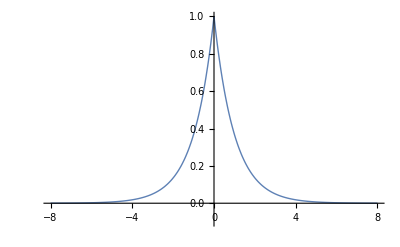

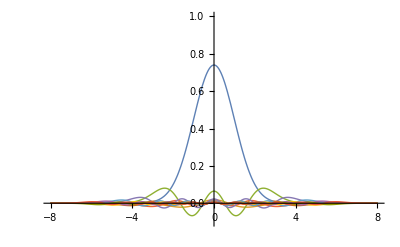

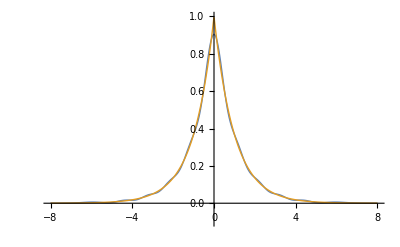

```mathematica
expMinusBetsAbsX = Plot[Block[{ α = 1, β = 1} , f[x]], {x, -8, 8}, PlotRange->{-0.1,1}, PlotStyle-> Thick]
expMinusBetsAbsXfirstOrderFitting = Plot[Block[{ α = 1, β = 1} , series] // Evaluate, {x, -8, 8}, PlotRange->{-0.1,1}, PlotStyle-> Thick]
expMinusBetsAbsXtenthOrderFitting = Plot[ Block[{ α = 1, β = 1}, {Total[series], f[x]}]  // Evaluate, {x, -8, 8}, PlotRange->{-0.1,1}, PlotStyle-> Thick]
```

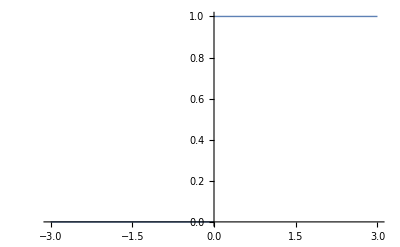

```mathematica
stepFunction = Plot[UnitStep[x],{x,-3,3},PlotStyle->Thick]
```

```mathematica
peeters`exportForLatex["expMinusBetsAbsX",expMinusBetsAbsX]
peeters`exportForLatex["expMinusBetsAbsXfirstOrderFitting",expMinusBetsAbsXfirstOrderFitting]
peeters`exportForLatex["expMinusBetsAbsXtenthOrderFitting",expMinusBetsAbsXtenthOrderFitting]
peeters`exportForLatex["stepFunction",stepFunction]
```

{expMinusBetsAbsX.eps,expMinusBetsAbsXpn.png}

{expMinusBetsAbsXfirstOrderFitting.eps,expMinusBetsAbsXfirstOrderFittingpn.png}

{expMinusBetsAbsXtenthOrderFitting.eps,expMinusBetsAbsXtenthOrderFittingpn.png}